## 65.1 mA

```mathematica
files = FileNames["65.1mA-*.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
fitdata = Table[Select[data[[i, 2]], #[[1]]≥ 0.0054 && #[[1]]≤0.013&], {i, 1, Length[data]}];
nlms = NonlinearModelFit[#, a - b ⅇ^(-c x), {a, b, c}, x]&/@fitdata;
funcs = Normal[#]&/@ nlms;
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

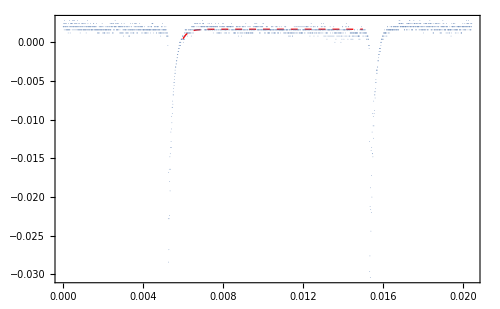
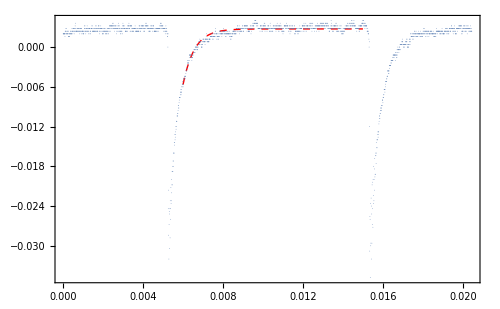
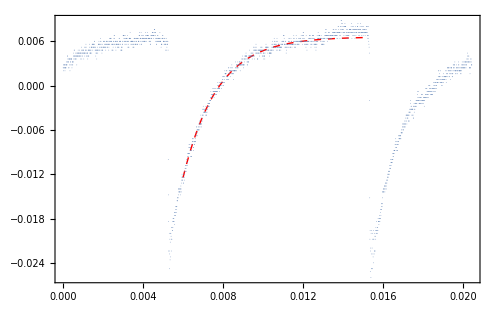
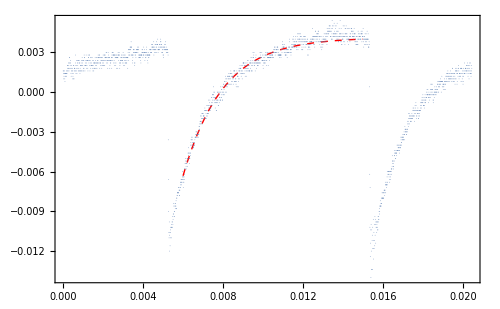
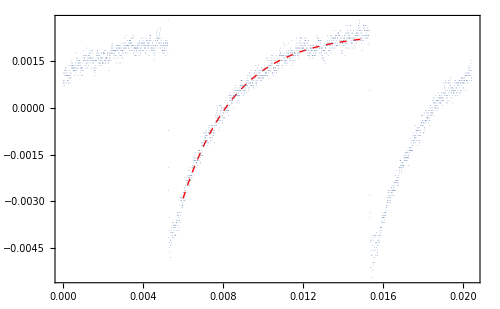
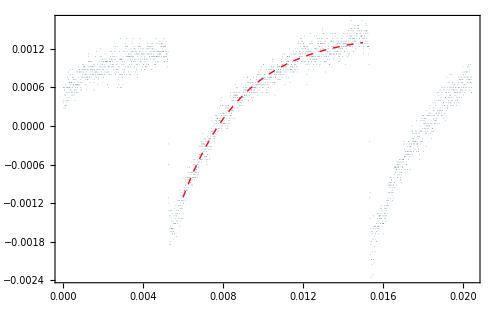
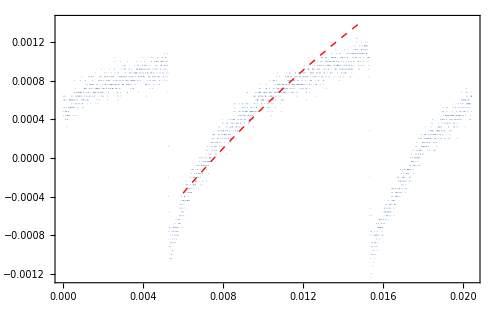
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[Plot[#[[2]], {x, 0.006, 0.015},ImageSize->500, PlotRange->All, Frame->True, PlotStyle->{Red, Dashed, Thick}], ListPlot[#[[1, 2]],PlotStyle->{PointSize[0.00001]}]]&/@ Transpose[{data, funcs}]
```

{3917.28,1739.92,1739.92,578.57,499.253,373.717,325.832,45.8084}

{{1.,3917.28},{0.399268,1739.92},{0.351649,1739.92},{0.152625,578.57},{0.0891333,499.253},{0.0512826,373.717},{0.0317461,325.832}}

FittedModel[185.374+3794.8 x]

| Estimate | Standard Error | t-Statistic | P-Value
a | 185.374 | 69.2978 | 2.67504 | 0.0440814
b | 3794.8 | 159.705 | 23.7613 | 2.45895×10^-6

5.39449

2.0166

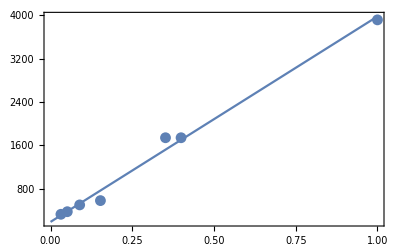

```mathematica
taus=#["ParameterTableEntries"][[3, 1]]&/@ nlms
filters = Drop[{0.,0.398736,0.453891,0.816374,1.04996,1.29003,1.49831,1.65801}, 0];
taudata = Drop[Transpose[{10^-filters, taus}],-1]

taufit = NonlinearModelFit[taudata, a + b x, {a, b}, x]
%["ParameterTable"]
10^3/(taufit["ParameterTableEntries"][[1,1]])
(taufit["ParameterTableEntries"][[1,2]] 10^3)/(taufit["ParameterTableEntries"][[1,1]])^2
Show[Plot[Normal[taufit], {x, 0, 1}, Frame->True, PlotRange->All], ListPlot[taudata]]
```

## 65.3 mA

```mathematica
files = FileNames["65.3mA-*.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
fitdata = Table[Select[data[[i, 2]], #[[1]]≥ 0.0054 && #[[1]]≤0.013&], {i, 1, Length[data]}];
nlms = NonlinearModelFit[#, a - b ⅇ^(-c x), {a, b, c}, x]&/@fitdata;
funcs = Normal[#]&/@ nlms;
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

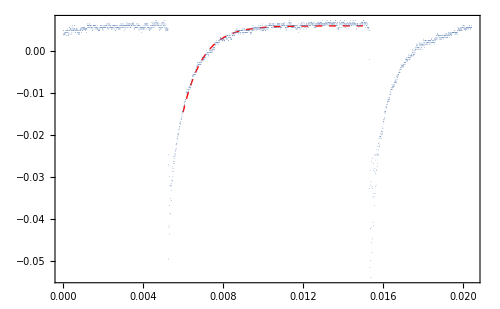
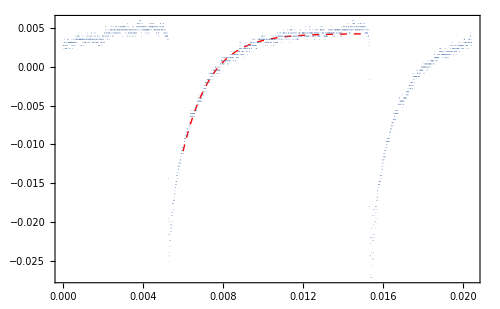
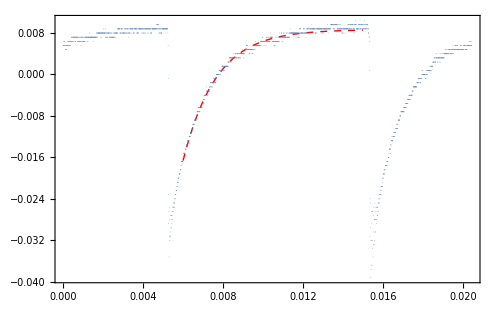
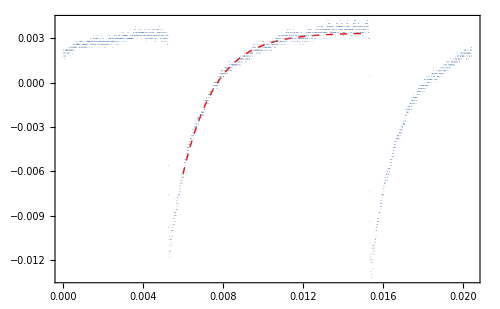
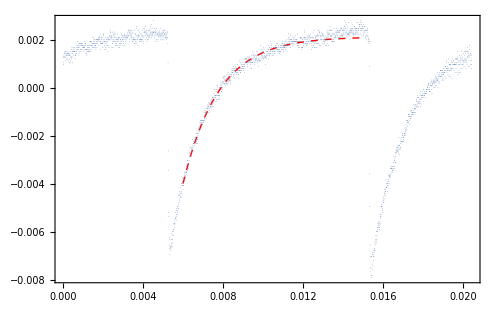
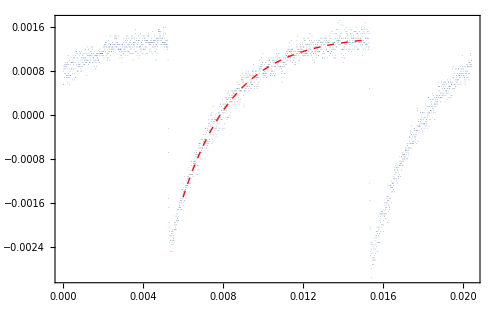
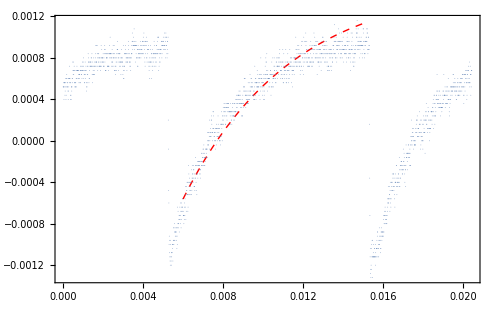
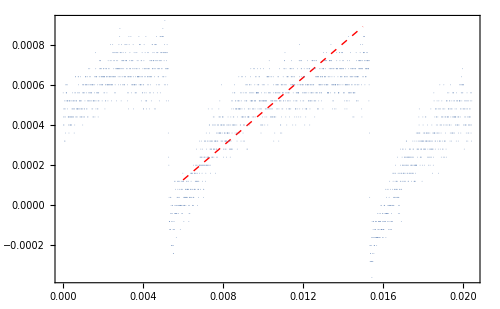

```mathematica
Show[Plot[#[[2]], {x, 0.006, 0.015},ImageSize->500, PlotRange->All, Frame->True, PlotStyle->{Red, Dashed, Thick}], ListPlot[#[[1, 2]],PlotStyle->{PointSize[0.00001]}]]&/@ Transpose[{data, funcs}]
```

{984.58,711.955,603.002,606.827,555.888,381.356,185.166,-0.37914}

{{1.,984.58},{0.399268,711.955},{0.351649,603.002},{0.152625,606.827},{0.0891333,555.888},{0.0512826,381.356}}

FittedModel[457.69+536.933 x]

| Estimate | Standard Error | t-Statistic | P-Value
a | 457.69 | 43.5187 | 10.5171 | 0.000462206
b | 536.933 | 92.8898 | 5.78033 | 0.0044494

2.18489

0.207746

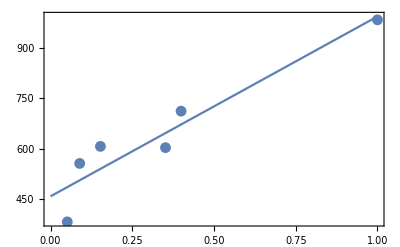

```mathematica
taus=#["ParameterTableEntries"][[3, 1]]&/@ nlms
filters = Drop[{0.,0.398736,0.453891,0.816374,1.04996,1.29003,1.49831,1.65801}, 0];

taudata = Drop[Transpose[{10^-filters, taus}],-2]
taufit = NonlinearModelFit[taudata, a + b x, {a, b}, x]
%["ParameterTable"]
10^3/(taufit["ParameterTableEntries"][[1,1]])
(taufit["ParameterTableEntries"][[1,2]] 10^3)/(taufit["ParameterTableEntries"][[1,1]])^2
Show[Plot[Normal[taufit], {x, 0, 1}, Frame->True, PlotRange->All], ListPlot[taudata]]
```

## 65.5 mA

```mathematica
files = FileNames["65.5mA-*.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
fitdata = Table[Select[data[[i, 2]], #[[1]]≥ 0.0054 && #[[1]]≤0.013&], {i, 1, Length[data]}];
nlms = NonlinearModelFit[#, a - b ⅇ^(-c x), {a, b, c}, x]&/@fitdata;
funcs = Normal[#]&/@ nlms;
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

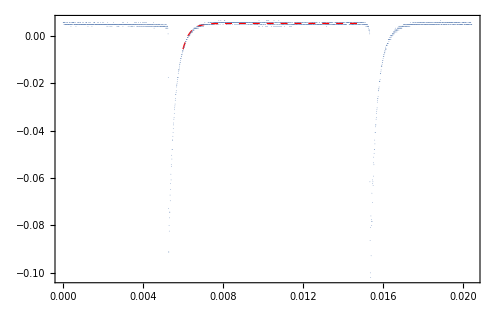
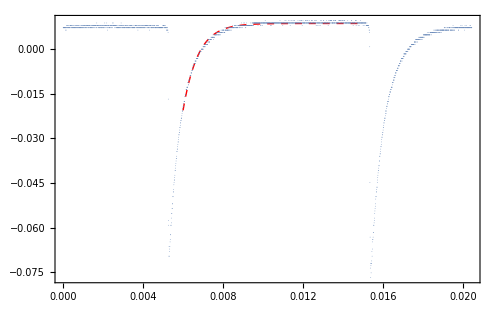
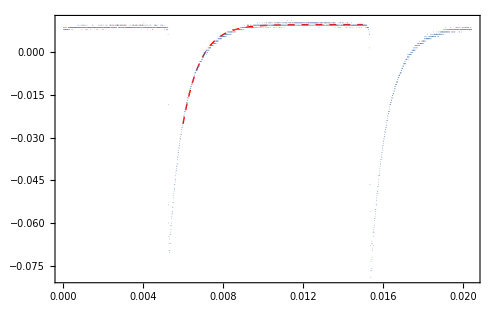
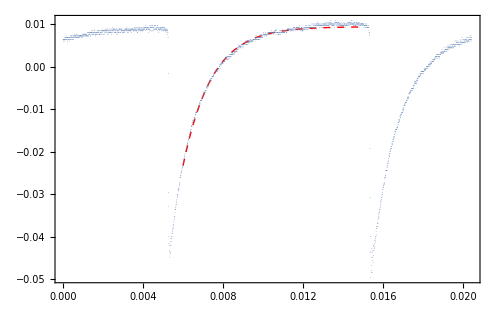
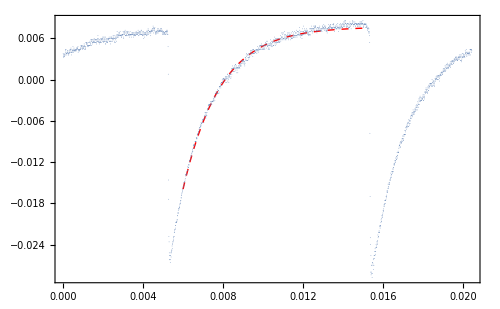
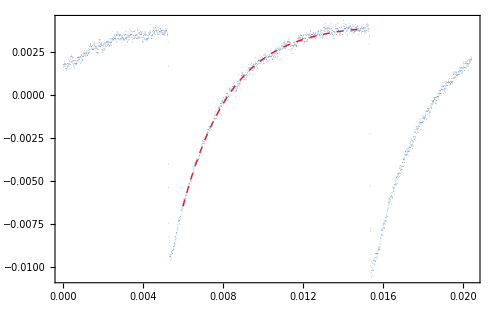
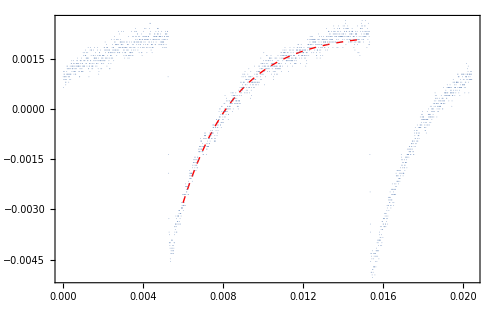
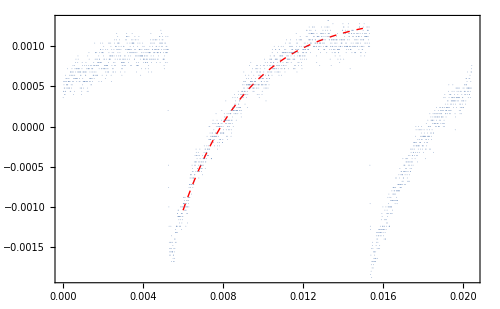

```mathematica
Show[Plot[#[[2]], {x, 0.006, 0.015},ImageSize->500, PlotRange->All, Frame->True, PlotStyle->{Red, Dashed, Thick}], ListPlot[#[[1, 2]],PlotStyle->{PointSize[0.00001]}]]&/@ Transpose[{data, funcs}]
```

{2887.68,1343.07,1145.25,696.361,534.244,414.737,376.383,294.205}

{{1.,2887.68},{0.399268,1343.07},{0.351649,1145.25},{0.152625,696.361},{0.0891333,534.244},{0.0512826,414.737},{0.0317461,376.383},{0.0219781,294.205}}

FittedModel[277.868+2607.16 x]

| Estimate | Standard Error | t-Statistic | P-Value
a | 277.868 | 14.6122 | 19.0162 | 1.3671×10^-6
b | 2607.16 | 35.9941 | 72.4328 | 4.66004×10^-10

3.59883

0.189251

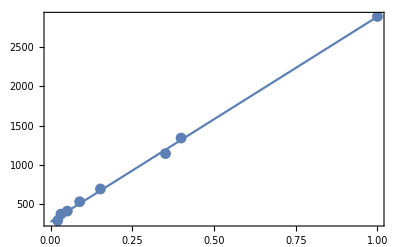

```mathematica
taus=#["ParameterTableEntries"][[3, 1]]&/@ nlms
filters = Drop[{0.,0.398736,0.453891,0.816374,1.04996,1.29003,1.49831,1.65801}, 0];
taudata = Transpose[{10^-filters, taus}]
taufit = NonlinearModelFit[taudata, a + b x, {a, b}, x]
%["ParameterTable"]
10^3/(taufit["ParameterTableEntries"][[1,1]])
(taufit["ParameterTableEntries"][[1,2]] 10^3)/(taufit["ParameterTableEntries"][[1,1]])^2
Show[Plot[Normal[taufit], {x, 0, 1}, Frame->True, PlotRange->All], ListPlot[taudata]]
```

## 65.7 mA

```mathematica
files = FileNames["65.7mA-*.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
fitdata = Table[Select[data[[i, 2]], #[[1]]≥ 0.0054 && #[[1]]≤0.013&], {i, 1, Length[data]}];
nlms = NonlinearModelFit[#, a - b ⅇ^(-c x), {a, b, c}, x]&/@fitdata;
funcs = Normal[#]&/@ nlms;
```

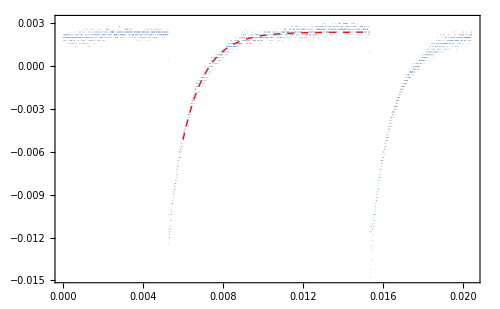
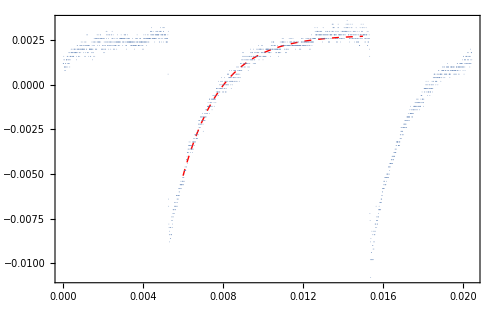
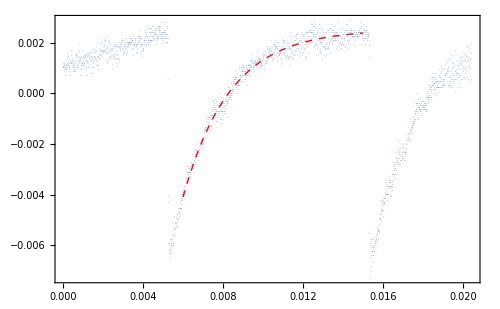
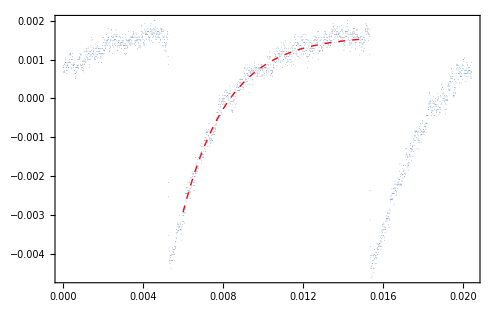
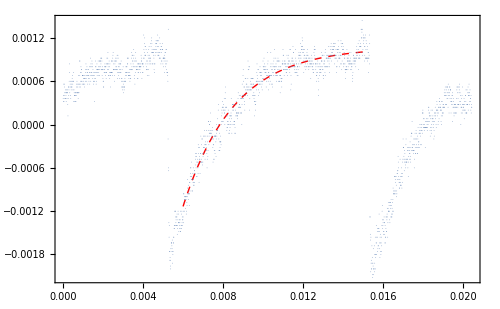
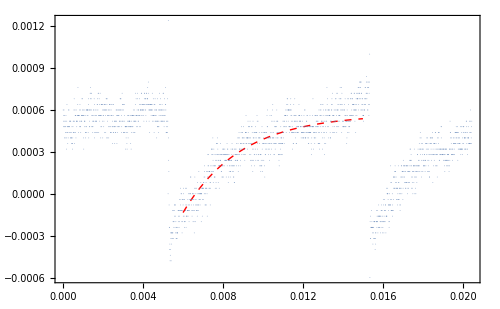

```mathematica
Show[Plot[#[[2]], {x, 0.006, 0.015},ImageSize->500, PlotRange->All, Frame->True, PlotStyle->{Red, Dashed, Thick}], ListPlot[#[[1, 2]],PlotStyle->{PointSize[0.00001]}]]&/@ Transpose[{data, funcs}]
```

{866.835,511.784,424.835,438.611,392.718,341.533}

{{1.,866.835},{0.399268,511.784},{0.351649,424.835},{0.152625,438.611},{0.0891333,392.718},{0.0512826,341.533}}

FittedModel[317.054+525.448 x]

| Estimate | Standard Error | t-Statistic | P-Value
a | 317.054 | 28.6664 | 11.0601 | 0.000380024
b | 525.448 | 61.188 | 8.58744 | 0.00101023

3.15404

0.285173

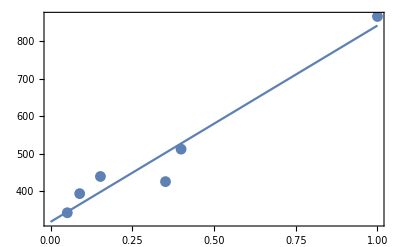

```mathematica
taus=#["ParameterTableEntries"][[3, 1]]&/@ nlms
filters = Drop[{0.,0.398736,0.453891,0.816374,1.04996,1.29003,1.49831,1.65801}, -2];
taudata = Transpose[{10^-filters, taus}]
taufit = NonlinearModelFit[taudata, a + b x, {a, b}, x]
%["ParameterTable"]
10^3/(taufit["ParameterTableEntries"][[1,1]])
(taufit["ParameterTableEntries"][[1,2]] 10^3)/(taufit["ParameterTableEntries"][[1,1]])^2
Show[Plot[Normal[taufit], {x, 0, 1}, Frame->True, PlotRange->All], ListPlot[taudata]]
```